Tue 24 Dec 2024 14:32:46GMT+9 Start_

########## control RAout拡大  ##########

4

5

0

500

1100

0.019

0.000025

1/10000

NDSolveValue::bcart: 警告：不十分な数の境界条件が独立変数xの方向に指定されました．解に人工境界の影響がある可能性があります．

{InterpolatingFunction[{{0., 5000.}, {0., 400.}}, <>],InterpolatingFunction[{{0., 5000.}, {0., 400.}}, <>]}

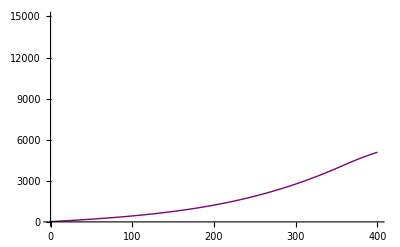

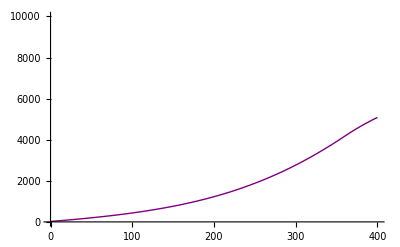

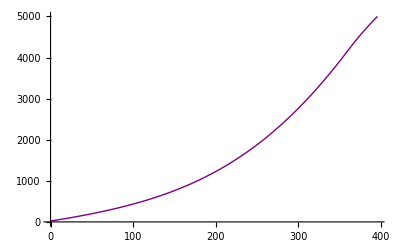

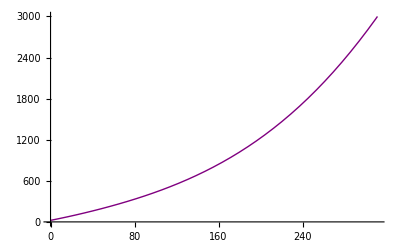

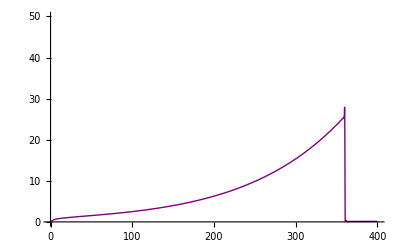

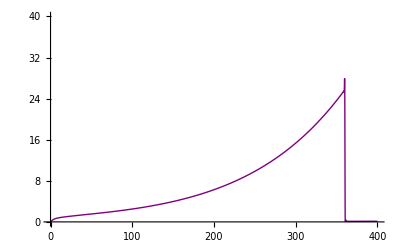

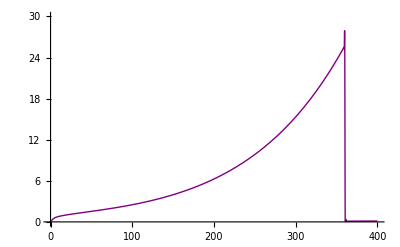

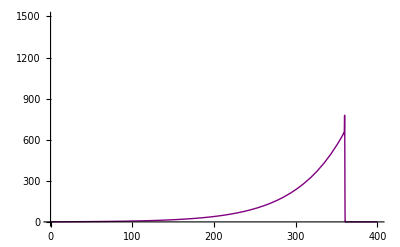

InterpolatingFunction::dmval: 入力値{1500,-39.991}は補間関数のデータ範囲外です．外挿が使用されます．

General::stop: この計算中に，InterpolatingFunction::dmvalのこれ以上の出力は表示されません．

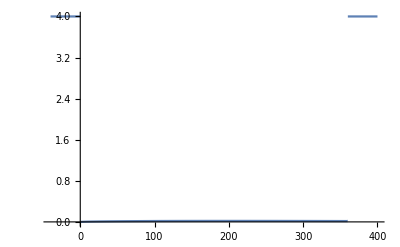

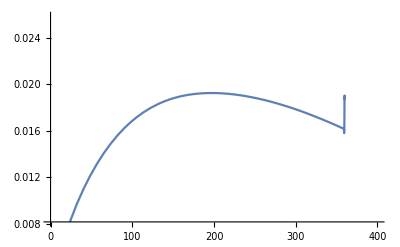

-Graphics3D-

-Graphics3D-

Solve::ifun: 逆関数がSolveで使われているため，求められない解がある可能性があります．解の詳細情報にはReduceをお使いください．

{}

Stopped Tue 24 Dec 2024 14:34:23GMT+9

```mathematica
Print[Start_ Now]

Print[
"########## control RAout拡大  ##########"
]

(*
control RAout拡大
*)
kmax = 4
vmax = 5
exRA = 0
kdeg = 500
f0 = 1100
lambda = 0.019
gamma = 2.5*10^(-5)
kp = 10^(-4)
(*関数定義*)
V[x_] := Which[x < 360, exRA, 360 <= x, vmax]
CypPLUS[v_, x_] := 
 kp + Which[x < 0, kmax, 0 <= x <= 360, 
   kdeg*(gamma*v^2)/(gamma*v^2 + 1 + f0*Exp[-lambda*(400 - x)]), 
   x > 360, kmax]
(*微分方程式定義*)
pde = {D[u[t, x], t] == 
    18*D[u[t, x], x, x] - 2*kp*u[t, x] + kp*v[t, x] + V[x], 
   D[v[t, x], t] == kp*u[t, x] - CypPLUS[v[t, x], x]*v[t, x]};
(*境界条件*)
bc = {u[0, x] == 0, v[0, x] == 0};
(*計算実行*)
{usol, vsol} = 
 NDSolveValue[{pde, bc }, {u, v}, {t, 0, 5000}, {x, 0, 400}, 
  MaxStepSize -> 0.5]

Plot[usol[1500, x], {x, 0, 400}, PlotStyle -> {Purple, Thick}, PlotRange -> {All, {0, 15000}}]
Plot[usol[1500, x], {x, 0, 400}, PlotStyle -> {Purple, Thick}, PlotRange -> {All, {0, 10000}}]
Plot[usol[1500, x], {x, 0, 400}, PlotStyle -> {Purple, Thick}, PlotRange -> {All, {0, 5000}}]
Plot[usol[1500, x], {x, 0, 400}, PlotStyle -> {Purple, Thick}, PlotRange -> {All, {0, 3000}}] 
Plot[vsol[1500, x], {x, 0, 400}, PlotStyle -> {Purple, Thick}, PlotRange -> {All, {0, 50}}]
Plot[vsol[1500, x], {x, 0, 400}, PlotStyle -> {Purple, Thick}, PlotRange -> {All, {0, 40}}]
Plot[vsol[1500, x], {x, 0, 400}, PlotStyle -> {Purple, Thick}, PlotRange -> {All, {0, 30}}]
Plot[vsol[1500, x]^2, {x, 0, 400}, PlotStyle -> {Purple, Thick}, PlotRange -> {All, {0, 1500}}]
Plot[CypPLUS[vsol[1500, x], x], {x, -40, 400}]
Plot[CypPLUS[vsol[1500, x], x], {x, 0, 400}]
Plot3D[usol[t, x], {t, 0, 1500}, {x, 0, 400}, PlotRange -> All]
Plot3D[vsol[t, x], {t, 0, 1500}, {x, 0, 400}, PlotRange -> All]

Solve[vsol[1500, x]^2 == 600,  x]

Print[Stopped Now]
```